## Initialization Code

```mathematica
qe = 1.60217663*10^-19;
e0 = 8.8541878188*10^-12;
kHz = 10^3;
MHz = 10^6;
nm = 10^-9;
μm = 10^-6;
mm = 10^-3;
amu = 1.66053904*10^-27;
r0 = 550 * μm;
κ = 0.077;
h = 6.62607015*10^-34;
ℏ = h/(2*π);
```

```mathematica
(*Calculate mass independent mathieu equations*)
getMathieuParams[knownSecFreqs_, knownMass_, ΩRF_]:= Module[{knownSecFreqsSorted, ar, az, qx},
knownSecFreqsSorted = knownSecFreqs[[Ordering[knownSecFreqs]]];
ar = 2/ΩRF^2*(knownSecFreqsSorted[[3]]^2-knownSecFreqsSorted[[2]]^2);
az = 4/ΩRF^2*knownSecFreqsSorted[[1]]^2;
qx = Sqrt[8*knownSecFreqsSorted[[3]]^2/ΩRF^2-(ar-2*az)];
{ar, az, qx}*knownMass
]
```

```mathematica
getMassIndepSecFreqs[massIndepMathieuParams_, massArr_, ΩRF_]:= Module[{arMassIndep, azMassIndep, qxMassIndep,
independentAxialFreqs, independentEGGsFreqs, independentRFFreqs},
arMassIndep = massIndepMathieuParams[[1]];
azMassIndep = massIndepMathieuParams[[2]];
qxMassIndep = massIndepMathieuParams[[3]];
independentAxialFreqs = Sqrt[azMassIndep/massArr*ΩRF^2/4];
independentEGGsFreqs = Sqrt[((qxMassIndep/massArr)^2+(arMassIndep/massArr-2*azMassIndep/massArr))*ΩRF^2/8];
independentRFFreqs= Sqrt[independentEGGsFreqs^2-ΩRF^2/2*arMassIndep/massArr];
{independentAxialFreqs, independentRFFreqs, independentEGGsFreqs}]
```

```mathematica
getPotential[massArr_, massIndepSecFreqs_, numIons_, EField_, ionPositions_,
β_:0]:=Module[{independentAxialFreqs, independentEGGsFreqs,independentRFFreqs,
Utrap, UColoumb, UField, Uanharmonic, U, EFieldMat},
EFieldMat =ConstantArray[EField, numIons];
independentAxialFreqs = massIndepSecFreqs[[1]];
independentRFFreqs = massIndepSecFreqs[[2]];
independentEGGsFreqs = massIndepSecFreqs[[3]];
Utrap = Sum[massArr[[i]]/2*amu*(independentRFFreqs[[i]]^2*x[i]^2+independentEGGsFreqs[[i]]^2*y[i]^2+independentAxialFreqs[[i]]^2*z[i]^2), {i, 1, numIons}];
UColoumb = qe^2/(4*π*e0)*Sum[Sum[ 1/Sqrt[(x[i]-x[j])^2+(y[i]-y[j])^2+(z[i]-z[j])^2], {i,1, j-1}], {j, 1, numIons}];
UField = -qe*Total[Flatten[ionPositions*EFieldMat]];
Uanharmonic = Sum[β*z[i]^3, {i, 1, numIons}];
U = Utrap+UColoumb+UField+Uanharmonic;
U
]
```

```mathematica
getEquilibriumPositions[U_,numIons_, ionEqPositions_] :=Module[{zGuess, guessPositions, ionEquilibriumPositions}, 
zGuess = 10*Flatten[Table[{i}, {i, -(numIons-1)/2, (numIons-1)/2,1}]]*μm;
guessPositions = Flatten[Table[{{z[i],zGuess[[i]]}, {y[i],0}, {x[i],0}}, {i,1,numIons}],1];
ionEquilibriumPositions = FindRoot[Table[D[U, q]==0, 
{q, Flatten[ionPositions]}],guessPositions];
ionEquilibriumPositions]
```

```mathematica
getModeParams[U_, massArr_, ionEquilibriumPositions_, numIons_,ionPositions_]:= Module[{evals, evecs,
M, H, orderingIndices, evecsSorted, evecsNormalized, evalsSorted, secFreqsMHz},
H = D[U, {Flatten[ionPositions], 2}]/.ionEquilibriumPositions;
M = DiagonalMatrix[Flatten[Table[massArr[[i]]*amu*{1,1,1}, {i, numIons}]]];
{evals, evecs} = Eigensystem[Sqrt[Inverse[M]].H.Sqrt[Inverse[M]]];
orderingIndices = Ordering[evals];
evecsSorted = evecs[[orderingIndices]];
evecsNormalized = Chop[Table[Normalize[evecsSorted[[idx]]], {idx, Length[evecsSorted]}]];
evalsSorted = evals[[orderingIndices]];
secFreqsMHz = Chop[Sqrt[evalsSorted]/(2*π*MHz)];
{evecsNormalized, secFreqsMHz}
]
```

```mathematica
overlapScore[axialRock_, vec_] := Abs[Conjugate[axialRock].vec]^2
getAxialRock[{vecs_, vals_}]:= Module[{axialRockBasis, scores, idx},
axialRockBasis = {0,0,-1,0,0,1,0,0,-1};
scores = overlapScore[axialRockBasis, #] & /@ vecs;
idx = First @ Ordering[scores, -1];
vals[[idx]]
]
```

```mathematica
SimDiffSecFreqs[Sec1_, Sec2_, Sec3_, voltRange_:20]:=Module[{singleIonSecFreqs, SecFreqs, maxSecFreqShift},
singleIonSecFreqs = 2*π*MHz*{Sec1, Sec2, Sec3};
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,voltRange/10}];
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, singleIonSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreqShift = (Max[secFreqs] - Min[secFreqs]);
maxSecFreqShift*MHz
]
```

```mathematica
getSecFreqs[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, β_:0]:= Module[{massIndepMathieuParams, massIndepSecFreqs, U, evecsNormalized, secFreqsMHz, ionEqPositions},
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, β];
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions] (*this must be a different name*);
{evecsNormalized, secFreqsMHz} = getModeParams[U, massArr, ionEqPositions, numIons,ionPositions];
{evecsNormalized, secFreqsMHz}
]
```

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3, 1.588}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

0.83944: {0.507896,0,0,-0.695761,0,0,0.507896,0,0}

1.08899: {0.707107,0,0,0,0,0,-0.707107,0,0}

1.22976: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.25658: {0,0.526166,0,0,-0.668055,0,0,0.526166,0}

1.38096: {0.491977,0,0,0.718273,0,0,0.491977,0,0}

1.42044: {0,0.707107,0,0,0,0,0,-0.707107,0}

1.66966: {0,-0.472386,0,0,-0.744112,0,0,-0.472386,0}

1.77196: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

## Check Mode Parameters for Tickling

### Ca - H^35Cl - Ca

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 2.6-.1, 2.6}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

1.22976: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.77196: {0,0,0.388271,0,0,-0.835758,0,0,0.388271}

2.36153: {-0.645027,0,0,0.409732,0,0,-0.645027,0,0}

2.39706: {0.707107,0,0,0,0,0,-0.707107,0,0}

2.469: {0,-0.648669,0,0,0.398067,0,0,-0.648669,0}

2.50118: {0,0.707107,0,0,0,0,0,-0.707107,0}

2.68039: {-0.289724,0,0,-0.912206,0,0,-0.289724,0,0}

2.78235: {0,-0.281476,0,0,-0.917357,0,0,-0.281476,0}

```mathematica
Total[evecsNormalized[[1]]] (*Axial COM*)
Total[evecsNormalized[[3]]] (*Axial ZigZag*)
```

1.73104

-0.0592165

### Ca - H_2^37 Cl - Ca

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
knownSecFreqs = 2*π*MHz*{.72, 2.6-.1, 2.6}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.722898: {0,0,0.58064,0,0,0.570713,0,0,0.58064}

1.24708: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.74822: {0,0,-0.403555,0,0,0.82115,0,0,-0.403555}

2.27803: {-0.478543,0,0,0.736202,0,0,-0.478543,0,0}

2.38877: {0,0.481279,0,0,-0.732626,0,0,0.481279,0}

2.39408: {0.707107,0,0,0,0,0,-0.707107,0,0}

2.49832: {0,0.707107,0,0,0,0,0,-0.707107,0}

2.52607: {-0.520573,0,0,-0.676762,0,0,-0.520573,0,0}

2.62618: {0,-0.518045,0,0,-0.680631,0,0,-0.518045,0}

```mathematica
Total[evecsNormalized[[1]]] (*Axial COM*)
Total[evecsNormalized[[3]]] (*Axial ZigZag*)
```

1.73199

0.0140397

### Ca - H_2^37 Cl

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
knownSecFreqs = 2*π*MHz*{.72, 2.6-.1, 2.6}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.724348: {0,0,0.715673,0,0,0.698436}

1.25479: {0,0,-0.698436,0,0,0.715673}

2.41776: {-0.874889,0,0,0.484323,0,0}

2.5216: {0,0.878984,0,0,-0.476851,0}

2.54259: {0.484323,0,0,0.874889,0,0}

2.64281: {0,-0.476851,0,0,-0.878984,0}

```mathematica
Total[evecsNormalized[[1]]] (*Axial COM*)
Total[evecsNormalized[[2]]] (*Axial OOP*)
```

1.41411

0.0172374

## Axial Rocking Mode Stray Field Shift

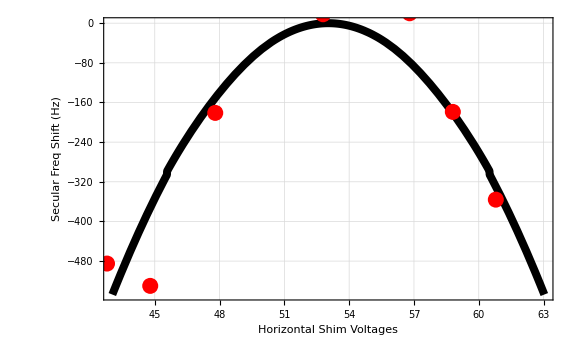

```mathematica
(*acutal data*)
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
actualVoltageList = {42.79, 62.79, 52.79, 44.79, 60.79, 47.8, 52.79, 57.8,55.79,52.79, 58.8, 56.8};
offsetSecFreqHz = {-485, -635, 18, -530, -356, -181, 72, 31, 82, 28, -179, 20};
actualData = Transpose@{actualVoltageList, offsetSecFreqHz};
voltRange = Max[actualVoltageList]-Min[actualVoltageList];
voltMidPoint = Mean[actualVoltageList];
nlm = NonlinearModelFit[actualData, -a*(x-b)^2+c,{a,b,c}, x, MaxIterations->1000];
voltMidPoint = ({a,b,c}/. nlm["BestFitParameters"])[[2]];

κ = 1.8;
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}],
ListPlot[Transpose@{actualVoltageList, offsetSecFreqHz}, PlotStyle->{Red, PointSize[0.02]}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

### Axial COM Mode Shift

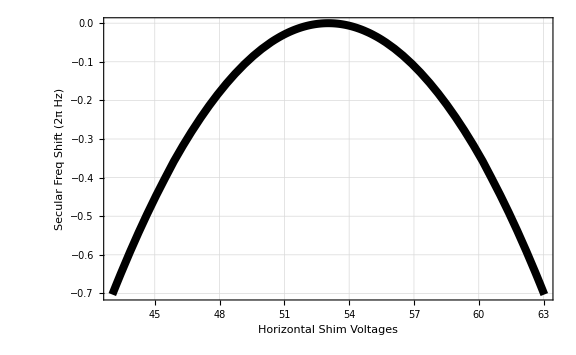

```mathematica
simVoltageList = Table[Voltage,  {Voltage, -voltRange/2+voltMidPoint, voltRange/2+voltMidPoint,0.1}];
secFreqs = Table[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[1]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];

Show[{Plot[(getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, knownSecFreqs, knownMass, numIons, ionPositions][[2]][[1]]- maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (2π Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

## Axial Rocking Mode Shift Dependence on Single Ion Secular Frequencies

### Scan Wide Range of Secular Frequencies

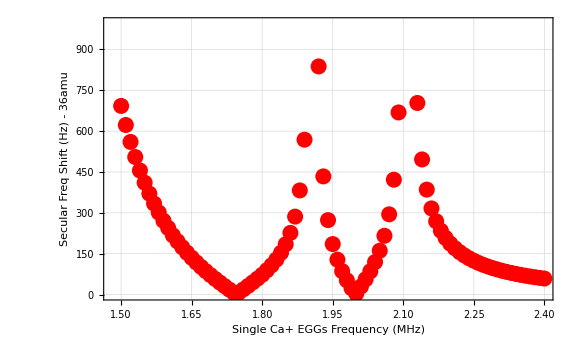

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
massArr = {knownMass, mUnknown, knownMass};
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.500, 2.40,.01}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.2,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
mass36Plot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz) - 36amu", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.93-.05, 1.93}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

1.22976: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.64332: {0.57476,0,0,-0.582496,0,0,0.57476,0,0}

1.70236: {0,-0.577948,0,0,0.576154,0,0,-0.577948,0}

1.74078: {-0.707107,0,0,0,0,0,0.707107,0,0}

1.77196: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

1.79466: {0,-0.707107,0,0,0,0,0,0.707107,0}

1.99239: {-0.411887,0,0,-0.812834,0,0,-0.411887,0,0}

2.04305: {0,-0.407402,0,0,-0.817341,0,0,-0.407402,0}

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\axial_zz_stray_field_shift36.jpg", mass36Plot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\axial_zz_stray_field_shift36.jpg

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
massArr = {knownMass, mUnknown, knownMass};
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.200, 3.000,.05}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.23,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
mass39Plot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz) - 39amu", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

-Graphics-

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\axial_zz_stray_field_shift39.jpg", mass39Plot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\axial_zz_stray_field_shift39.jpg

### Scan Narrowly about “nulls” where shift vanishes

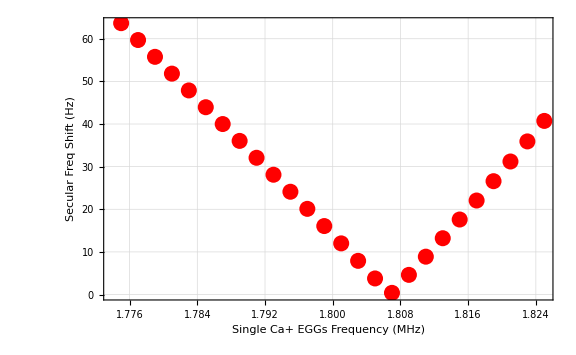

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.775, 1.825,.002}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
firstNullPlot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\first_null_plot.jpg", firstNullPlot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\first_null_plot.jpg

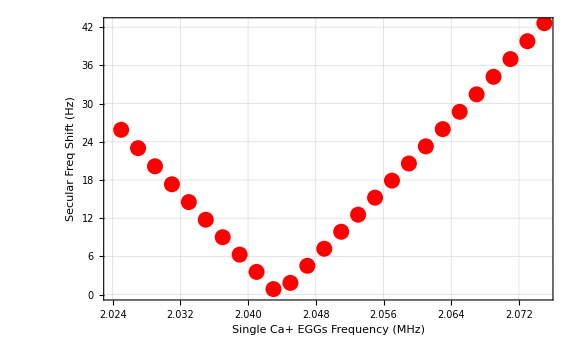

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 2.025, 2.075,.002}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
secondNullPlot = ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

#### Scan narrowly about ‘resonances’

```mathematica
Export["\\\\eric.physics.ucla.edu\\groups\\motion\\Mathematica\\cat_interferometer\\images\\second_null_plot.jpg", secondNullPlot]
```

\\eric.physics.ucla.edu\groups\motion\Mathematica\cat_interferometer\images\second_null_plot.jpg

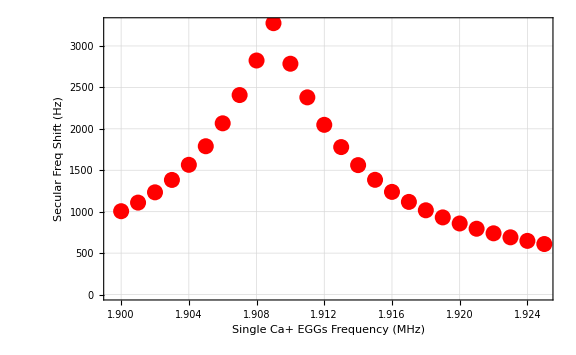

```mathematica
eggFreqSpan = Table[eggsFreq, {eggsFreq, 1.9, 1.925,.001}];
freqShift = Table[SimDiffSecFreqs[.710,eggsFreq-.3,eggsFreq], {eggsFreq, eggFreqSpan}];
shiftData = Transpose@{eggFreqSpan, freqShift};
ListPlot[shiftData, PlotStyle->{Red, PointSize[0.02]},
FrameLabel->{Style["Single Ca+ EGGs Frequency (MHz)", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic]
```

### See trend of stray fields and shift caused for different secular frequency configurations

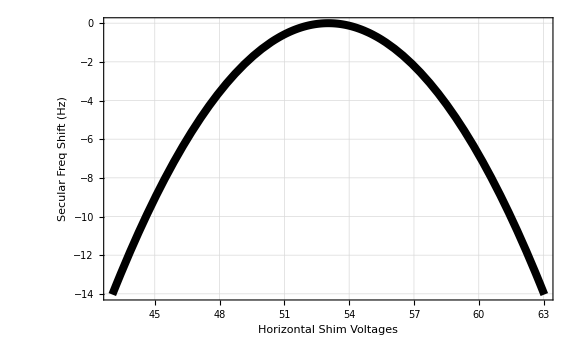

```mathematica
testSecFreqs = 2*π*{.71, 1.5, 1.8}*MHz;
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

```mathematica
testSecFreqs = 2*π*{.71, 1.8, 2.1}*MHz;
secFreqs = Table[getAxialRock[getSecFreqs[{(κ*(Volt-voltMidPoint))/Sqrt[2],(κ*(Volt-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]], {Volt, simVoltageList}];
maxSecFreq = Max[secFreqs];


Show[{Plot[(getAxialRock[getSecFreqs[{(κ*(Voltage-voltMidPoint))/Sqrt[2],(κ*(Voltage-voltMidPoint))/Sqrt[2],0}, massArr, testSecFreqs, knownMass, numIons, ionPositions]]-maxSecFreq)*MHz,
{Voltage, -voltRange/2+voltMidPoint,voltRange/2+voltMidPoint}, PlotStyle->{Black, Thickness->0.01}]},
FrameLabel->{Style["Horizontal Shim Voltages", 16], Style["Secular Freq Shift (Hz)", 16]}, ImageSize->Large, Frame->{{True, False}, {True, False}},
GridLines->Automatic
]
```

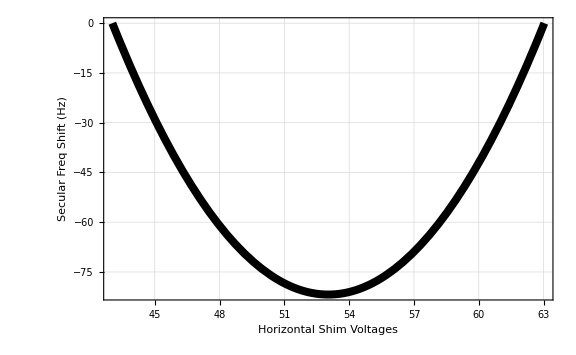

## Coulomb Anharmonic Calculations

### Initialization Code

```mathematica
ll[q_, secFreqsMHz_]:= Sqrt[ℏ/(2*2*π*secFreqsMHz[[q]]*MHz)];
quarticDiagonalTerms[nList_, G4_,  secFreqsMHz_, numModes_]:=Sum[ll[i,secFreqsMHz]^4*G4[[i,i,i,i]]*(6*nList[[i]]^2+6*nList[[i]]+3), {i,1,numModes}]
quarticOffDiagonalTerms[nList_, G4_,  secFreqsMHz_, numModes_]:=Sum[6*ll[i, secFreqsMHz]^2*ll[j, secFreqsMHz]^2*G4[[i,i,j,j]]*(2*nList[[i]]+1)*(2*nList[[j]]+1), 
													{i,1,numModes-1},
													{j,i+1,numModes}]
firstOrderPert[nList_, G4_, secFreqsMHz_, numModes_]:= (quarticDiagonalTerms[nList, G4,  secFreqsMHz, numModes] 
													+ quarticOffDiagonalTerms[nList, G4,  secFreqsMHz, numModes]);
```

```mathematica
(*Construct Matrix Elements*)
x3Element[m_, n_]:= (Sqrt[(n+1)*(n+2)*(n+3)]*KroneckerDelta[m, n+3]
								+3*(n+1)^(3/2)*KroneckerDelta[m, n+1]
								+ 3*n^(3/2)*KroneckerDelta[m, n-1]
								+ Sqrt[(n)*(n-1)*(n-2)]*KroneckerDelta[m, n-3]
								);
x2Element[m_, n_]:= (Sqrt[(n+1)*(n+2)]*KroneckerDelta[m,n+2]
					+ (2*n+1)*KroneckerDelta[m, n]
					+ Sqrt[n*(n-1)]*KroneckerDelta[m, n-2]
					);								
x1Element[m_, n_]:= Sqrt[n+1]KroneckerDelta[m,n+1] + Sqrt[n]*KroneckerDelta[m,n-1];	

				
(*Construct Amplitudes*)											
cubicDiagonalTerm[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= Sum[G3[[i,i,i]]*ll[i, secFreqsMHz]^3*
										x3Element[mList[[i]], nList[[i]]]*
										Product[KroneckerDelta[mList[[q]], nList[[q]]], {q, DeleteCases[Range[numModes], i]}]
										,
										{i, 1, numModes}];
cubicOffDiagonalTerm[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= (Sum[3*G3[[i,j,j]]*ll[j, secFreqsMHz]^2*ll[i,secFreqsMHz]
										* x1Element[mList[[i]], nList[[i]]]
										* x2Element[mList[[j]], nList[[j]]]
										* Product[
									        KroneckerDelta[mList[[q]], nList[[q]]],
									        {q, Complement[Range[numModes], {i, j}]}]
									    + 3*G3[[i,i,j]]*ll[i, secFreqsMHz]^2*ll[j, secFreqsMHz]*
										x1Element[mList[[j]], nList[[j]]]* x2Element[mList[[i]], nList[[i]]]
										*  Product[
									        KroneckerDelta[mList[[q]], nList[[q]]],
									        {q, Complement[Range[numModes], {i, j}]}
									     ],
										{i, 1, numModes-1},
										{j, i+1, numModes}
										]
										+ 
										Sum[
										6*G3[[i,j,k]]*ll[i, secFreqsMHz]*ll[j, secFreqsMHz]*ll[k, secFreqsMHz]
										* x1Element[mList[[i]], nList[[i]]]
										* x1Element[mList[[j]], nList[[j]]] 
										* x1Element[mList[[k]], nList[[k]]]
										* Product[
								        KroneckerDelta[mList[[q]], nList[[q]]],
								        {q, Complement[Range[numModes], {i, j, k}]}],
										{i, 1, numModes-2},
										{j, i+1, numModes-1},
										{k, j+1, numModes}]
										);
										
cubicMatrixElement[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= (cubicDiagonalTerm[mList, nList, G3,  secFreqsMHz, numModes] 
																+ cubicOffDiagonalTerm[mList, nList, G3,  secFreqsMHz, numModes]);

secOrderPertEle[mList_, nList_, G3_, secFreqsMHz_, numModes_]:= Abs[cubicMatrixElement[mList, nList, G3,  secFreqsMHz, numModes]]^2/(Total[ℏ*2*π*MHz*secFreqsMHz*nList]-Total[ℏ*2*π*MHz*secFreqsMHz*mList]);
secOrderPert[intermediateStates_, nList_, G3_,  secFreqsMHz_, numModes_]:=Sum[
secOrderPertEle[mList, nList, G3,  secFreqsMHz, numModes], 
{mList, intermediateStates}
]
```

```mathematica
(*Create all connected basis states to a nList*)

createCandidateStates[nList_, numModes_]:=Module[{states},
	states = {};
	(*x3 term all excitations on one mode*);
	Do[
	states = Join[states, 
	Table[
	nList+d*UnitVector[numModes, q], 
	{d, {-3,-1,1,3}}
	]
	],
	{q, 1, numModes}
	];
	(*1 x2 term and 1 x1 term - two excitations on one mode and one excitations one another mode*)
	Do[
	states = Join[states, 
	Catenate @ Table[
	nList
	+di*UnitVector[numModes, q1]
	+dj*UnitVector[numModes, q2],
	{di, {-2,0,2}},
	{dj, {-1,1}}
	]
	],
	{q1, 1, numModes-1},
	{q2, q1+1, numModes}
	];
	Do[
	states = Join[states, 
	Catenate @ Table[
	nList
	+di*UnitVector[numModes, q2]
	+dj*UnitVector[numModes, q1],
	{di, {-2,0,2}},
	{dj, {-1,1}}
	]
	],
	{q1, 1, numModes-1},
	{q2, q1+1, numModes}
	];
	(*3 x1 terms -  all excitations on different modes*);
	Do[
	states = Join[states, 
	Catenate @ Catenate @ Table[
	nList
	+di*UnitVector[numModes, q1]
	+dj*UnitVector[numModes, q2]
	+dk*UnitVector[numModes, q3],
	{di, {-1,1}},
	{dj, {-1,1}},
	{dk, {-1,1}}
	]
	],
	{q1, 1, numModes-2},
	{q2, q1+1, numModes-1},
	{q3, q2+1, numModes}
	];
	states = Select[states, Min[#]>=0 &];
	DeleteDuplicates[states]
	]
```

```mathematica
getPerturbationTensors[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, β_:0]:=
 Module[
 {massIndepMathieuParams, massIndepSecFreqs, U, evecsNormalized, secFreqsMHz, ionEqPositions,
 coordMasses, U3, A3, A4, B3temp, C3temp, U4, B4temp, C4temp, D4temp, G3, G4},
massIndepMathieuParams= getMathieuParams[knownSecFreqs, knownMass, ΩRF];
massIndepSecFreqs = getMassIndepSecFreqs[massIndepMathieuParams, massArr, ΩRF];
U = getPotential[massArr, massIndepSecFreqs, numIons, EField, ionPositions, β];
coordMasses=Flatten[ConstantArray[#,Length[First[ionPositions]]]&/@ massArr] *amu;
ionEqPositions = getEquilibriumPositions[U, numIons, ionPositions] (*this must be a different name*);
{evecsNormalized, secFreqsMHz} = getModeParams[U, massArr, ionEqPositions, numIons,ionPositions];
U3 = D[U, {Flatten[ionPositions], 3}]/.ionEqPositions;
U4 = D[U, {Flatten[ionPositions], 4}]/.ionEqPositions;
A3 = U3/(3! Sqrt[Outer[Times, coordMasses, coordMasses, coordMasses]]);
A4 = U4/(4! Sqrt[Outer[Times, coordMasses, coordMasses, coordMasses, coordMasses]]);

B3temp = TensorContract[TensorProduct[A3, evecsNormalized], {{1, 5}}];
C3temp = TensorContract[TensorProduct[B3temp, evecsNormalized], {{1, 5}}];
G3 = TensorContract[TensorProduct[C3temp, evecsNormalized], {{1, 5}}];

B4temp = TensorContract[TensorProduct[A4, evecsNormalized], {{1, 6}}];
C4temp = TensorContract[TensorProduct[B4temp, evecsNormalized], {{1, 6}}];
D4temp = TensorContract[TensorProduct[C4temp, evecsNormalized], {{1, 6}}];
G4 = TensorContract[TensorProduct[D4temp, evecsNormalized], {{1, 6}}];
{G3, G4, secFreqsMHz}
]
```

```mathematica
calcSecFreqShifts[nList_, q_, G3_, G4_, secFreqsMHz_]:= Module[
{intermediateStates, intermediateStatesExcited, excitedState, shift, numModes},
	numModes = Length[nList];
	excitedState = nList + UnitVector[numModes, q];
	intermediateStates = DeleteCases[createCandidateStates[nList, numModes], nList];
	intermediateStatesExcited = DeleteCases[createCandidateStates[excitedState, numModes], excitedState];
	shift = 
	(firstOrderPert[excitedState, G4, secFreqsMHz, numModes] + secOrderPert[intermediateStatesExcited, excitedState, G3, secFreqsMHz, numModes]) /(2*π*ℏ) 
	- (firstOrderPert[nList, G4, secFreqsMHz, numModes] + secOrderPert[intermediateStates, nList, G3, secFreqsMHz, numModes]) /(2*π*ℏ)
]
```

```mathematica
getSecFreqShifts[EField_, 
massArr_, knownSecFreqs_, knownMass_, numIons_, ionPositions_, nList_, q_:1, β_:0]:=
 Module[
 {shift, G3, G4, secFreqsMHz},
 {G3, G4, secFreqsMHz} = getPerturbationTensors[EField, 
	massArr, knownSecFreqs, knownMass, numIons, ionPositions, β];
shift = calcSecFreqShifts[nList, q, G3, G4, secFreqsMHz]
]
```

### Check Roos (https://arxiv.org/pdf/0705.0788)

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
knownSecFreqs = 2*π*MHz*{1.7, 4, 4}; 
massArr = {knownMass, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
nList = {0,0,0,0,0,0};
```

```mathematica
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

1.7: {0,0,0.707107,0,0,0.707107}

2.94449: {0,0,-0.707107,0,0,0.707107}

3.62077: {0.465608,-0.532174,0,-0.465608,0.532174,0}

3.62077: {0.532174,0.465608,0,-0.532174,-0.465608,0}

4.: {-0.514148,-0.48544,0,-0.514148,-0.48544,0}

4.: {-0.48544,0.514148,0,-0.48544,0.514148,0}

{-2.605,-4.28582,-6.03923,-10.0395,-15.9123}

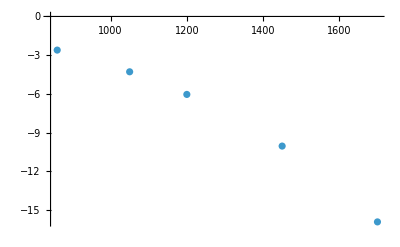

```mathematica
axialSecFreqs = {.86, 1.05, 1.2, 1.45, 1.7};
secShifts = Table[getSecFreqShifts[EField, 
massArr, 2*π*MHz*{axialSecFreqs[[s]], 4, 4}, knownMass, numIons, ionPositions,nList + UnitVector[6,3], 2,0]- 
getSecFreqShifts[EField, massArr, 2*π*MHz*{axialSecFreqs[[s]], 4, 4}, knownMass, numIons, ionPositions,nList, 2,0],{s, 1, Length[axialSecFreqs]}]
a = Thread[{axialSecFreqs(kHz), secShifts}];
ListPlot[a]
```

### Secular Frequency Shift for Ca - H35Cl - Ca as we Heat Chain

```mathematica
knownMass = 39.962590863; 
mUnknown = 36;
knownSecFreqs = 2*π*MHz*{.65, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.660856: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

0.984751: {0.529487,0,0,-0.662788,0,0,0.529487,0,0}

1.12583: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.15369: {0.707107,0,0,0,0,0,-0.707107,0,0}

1.35849: {0,0.549796,0,0,-0.628847,0,0,0.549796,0}

1.40872: {-0.468662,0,0,-0.748807,0,0,-0.468662,0,0}

1.47252: {0,-0.707107,0,0,0,0,0,0.707107,0}

1.62222: {0,0,0.388271,0,0,-0.835758,0,0,0.388271}

1.69573: {0,-0.444662,0,0,-0.777529,0,0,-0.444662,0}

#### Axial Stretch/Zigzag (1,-1,1) Mode

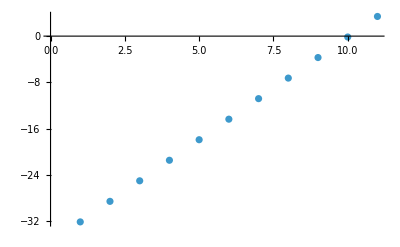

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 9], 9,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

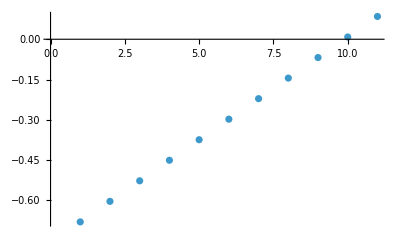

```mathematica
knownSecFreqs = 2*π*MHz*{.65, 2.2, 2.4};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 9], 9,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

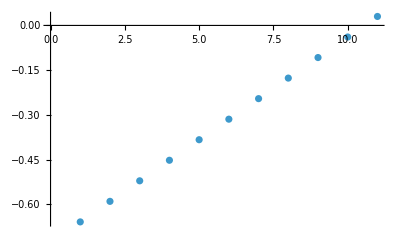

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 2.2, 2.4};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 9], 9,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

#### Axial COM (1,1,1) Mode

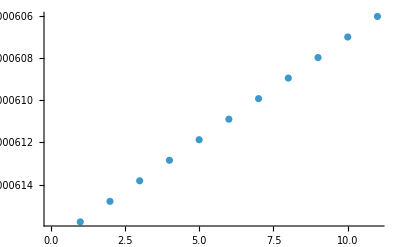

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 2.2, 2.4};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsCOM = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 1], 1,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsCOM],
{"Axial COM Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

### Secular Frequency Shift for Ca - H2 37Cl - Ca as we Heat Chain

```mathematica
knownMass = 39.962590863; 
mUnknown = 39;
knownSecFreqs = 2*π*MHz*{.71, 1.3242, 1.6096}; (*Frequencies from Hao's Calibration on 06-04 - keep these and if need to change override later*)
massArr = {knownMass, mUnknown, knownMass};
EField ={0,0,0};
numIons = Length[massArr];
ionPositions = Table[{x[i], y[i], z[i]}, {i, numIons}];
ΩRF = 2*π*19.0696 * MHz;
{evecsNormalized, secFreqsMHz} = getSecFreqs[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions];

Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.712858: {0,0,0.58064,0,0,0.570713,0,0,0.58064}

0.774205: {0.431016,0,0,-0.792748,0,0,0.431016,0,0}

1.11777: {0.707107,0,0,0,0,0,-0.707107,0,0}

1.20399: {0,-0.435707,0,0,0.787603,0,0,-0.435707,0}

1.22976: {0,0,-0.707107,0,0,0,0,0,0.707107}

1.33945: {-0.560558,0,0,-0.609549,0,0,-0.560558,0,0}

1.44455: {0,0.707107,0,0,0,0,0,-0.707107,0}

1.62456: {0,-0.55692,0,0,-0.616183,0,0,-0.55692,0}

1.72394: {0,0,-0.403555,0,0,0.82115,0,0,-0.403555}

#### Axial Stretch/Zigzag (1,-1,1) Mode

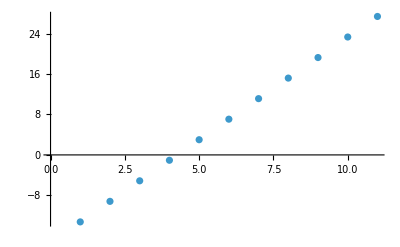

```mathematica
knownSecFreqs = 2*π*MHz*{.81, 1.3242, 1.6096};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 9], 9,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

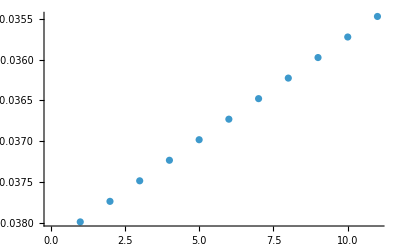

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 2.2, 2.4};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsRock = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 9], 9,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsRock],
{"Axial Rocking Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

#### Axial COM (1,1,1) Mode

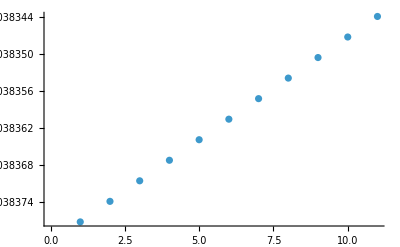

```mathematica
knownSecFreqs = 2*π*MHz*{.71, 2.2, 2.4};
nMax = 10;
nList = ConstantArray[0,9];
secShiftsCOM = Table[getSecFreqShifts[EField, 
massArr,knownSecFreqs, knownMass, numIons, ionPositions,nList + s*UnitVector[9, 1], 1,0],{s, 0,nMax}];
Labeled[ListPlot[secShiftsCOM],
{"Axial COM Secular Frequency Shift", "Phonon Number" }, {Left, Top}, RotateLabel->{True, False}]
```

### Dispersive Shift Calculations, i.e. how radial mode phonons affect axial stretch/COM mode

```mathematica
Table[Print[secFreqsMHz[[i]], ": ", evecsNormalized[[i]]], {i, 1, Length[secFreqsMHz]}];
```

0.721858: {0,0,0.59097,0,0,0.549098,0,0,0.59097}

0.880627: {0.511005,0,0,-0.691194,0,0,0.511005,0,0}

1.11777: {-0.707107,0,0,0,0,0,0.707107,0,0}

1.22976: {0,0,0.707107,0,0,0,0,0,-0.707107}

1.2865: {0,-0.529234,0,0,0.663191,0,0,-0.529234,0}

1.40659: {0.488748,0,0,0.72267,0,0,0.488748,0,0}

1.44455: {0,-0.707107,0,0,0,0,0,0.707107,0}

1.69283: {0,-0.468947,0,0,-0.74845,0,0,-0.468947,0}

1.77196: {0,0,-0.388271,0,0,0.835758,0,0,-0.388271}

```mathematica
allModesCooled = {0,0,0,0,0,0,0,0,0};
radialModesHot = {0,3,3,0,3,3,3,3,0};
getSecFreqShifts[EField, 
massArr, knownSecFreqs, knownMass, numIons, ionPositions,allModesCooled , 9,0]- 
getSecFreqShifts[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions,radialModesHot, 9,0]
```

219.327

```mathematica
allModesCooled = {0,0,0,0,0,0,0,0,0};
radialRockModesHot = {0,3,3,0,3,0,3,0,0};
getSecFreqShifts[EField, 
massArr, knownSecFreqs, knownMass, numIons, ionPositions,allModesCooled , 9,0]- 
getSecFreqShifts[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions,radialRockModesHot, 9,0]
```

215.308

```mathematica
allModesCooled = {0,0,0,0,0,0,0,0,0};
radialCOMModesHot = {0,0,0,0,0,3,0,3,0};
getSecFreqShifts[EField, 
massArr, knownSecFreqs, knownMass, numIons, ionPositions,allModesCooled , 9,0]- 
getSecFreqShifts[EField, massArr, knownSecFreqs, knownMass, numIons, ionPositions,radialCOMModesHot, 9,0]
```

4.01915

## Cubic Anharmonic Calculations (Normal modes of trapped ions in the presence of anharmonic trap potentials - https://arxiv.org/abs/1105.4752 ) Ions of same mass

### Ions of same mass

```mathematica
ωc[κ_, m_, λ_]:= Module[
{},
l = (qe/(8*π*e0*κ))^(1/3);
Sqrt[(2*qe*κ)/(m*amu)]*(1-9/2^(7/3)(l/λ)^2)]
ωs[κ_, m_, λ_]:= Module[
{},
l = (qe/(8*π*e0*κ))^(1/3);
Sqrt[(6*qe*κ)/(m*amu)]*(1-3/2^(7/3)(l/λ)^2)]
```

```mathematica
ωc[4.15, 40, 10^10]/(2*π)
ωs[4.15, 40, 10^10]/(2*π)
```

0.0724985 √(qe/amu) (1-8.05961×10^-22 (qe/e0)^(2/3))

0.125571 √(qe/amu) (1-2.68654×10^-22 (qe/e0)^(2/3))

### Ions of unequal mass

```mathematica
ωp[κ_, μ_, m1_, λ_]:= Module[
{},
l = (qe/(8*π*e0*κ))^(1/3);
Sqrt[(2*qe*κ)/(m1*amu)]*Sqrt[1+μ+Sqrt[μ^2-μ+1]]*(1-3/2^(8/3)*(1-μ)/Sqrt[μ^2-μ+1]*l/λ)
]
ωm[κ_, μ_, m1_, λ_]:= Module[
{},
l = (qe/(8*π*e0*κ))^(1/3);
Sqrt[(2*qe*κ)/(m1*amu)]*Sqrt[1+μ-Sqrt[μ^2-μ+1]]*(1+3/2^(8/3)*(1-μ)/Sqrt[μ^2-μ+1]*l/λ)
]
```

### Home’s Calculations

```mathematica
κh = 1.3*10^7;
ωm[κh, 1, 9, 10^10]/(2*π) (*Berylium ions*)
ωm[κh, 9/24,9,10^10]/(2*π)
ωp[κh, 9/24, 9, 10^10]/(2*π)
```

2.65715×10^6

1.87889×10^6

3.98573×10^6

```mathematica
ωm[κh, 9/24, 9, 230*10^-6]/(2*π)-ωm[κh, 24/9, 24, 230*10^-6]/(2*π)
```

21017.3

### Our Results

```mathematica
κc = 4.15*10^6;
ωm[κc, 1, 40, 10^10]/(2*π*MHz) (*Ca ions*)
ωm[κc, 40/39,40,10^10]/(2*π*MHz)
ωp[κc, 39/40, 40, 10^10]/(2*π*MHz)
```

0.712131

0.716595

1.22576

```mathematica
ωm[κc, 39/40, 39, 30*10^-3]/(2*π)-ωm[κc, 40/39, 40, 30*10^-3]/(2*π)
ωp[κc, 39/40, 39, 3*10^-3]/(2*π)-ωp[κc, 40/39, 40, 3*10^-3]/(2*π)
```

3.18625

-55.1964